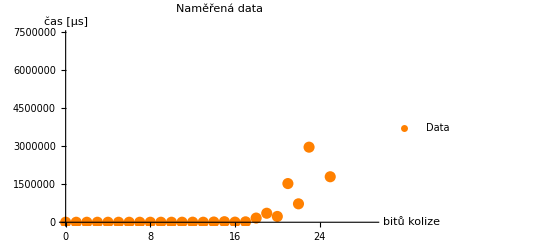

{a→0.00002403,b→1.4903}

Model doby hledání x bitů kolize: 0.00002403 2^(1.4903 x)

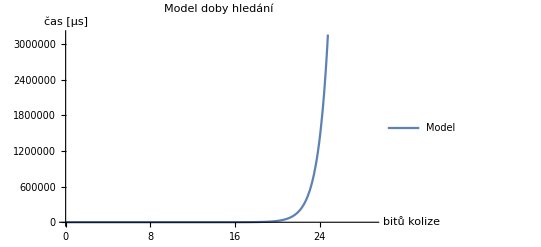

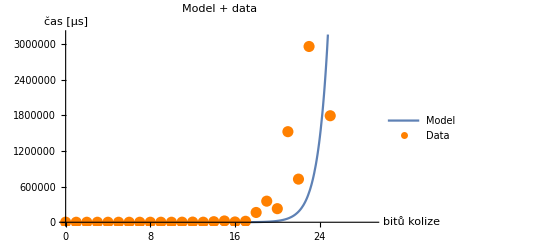

512 bitů kolize se bude hledat: 1.19238×10^225

Čas od veľkého tresku: 4.3×10^23 μs

```mathematica
(*data ve formátu:{{počet bitů kolize,doba hledání},{.,.},...}*)data={{0,1403},{1,8},{2,6},{3,5},{4,15},{5,8},{6,6},{7,65},{8,203},{9,245},{10,28},{11,1189},{12,2874},{13,910},{14,9295},{15,21535},{16,4867},{17,16302},{18,164632},{19,354822},{20,228620},{21,1524028},{22,725792},{23,2957543},{24,15653716},{25,1792145},{26,28202397},{27,29865983},{28,81107987},{29,247588184}};
varListPlot=ListPlot[data,PlotLabel->"Naměřená data",AxesLabel->{"bitů kolize","čas [μs]"},PlotStyle->{Orange,PointSize[0.02]},PlotLegends->{"Data"}]

(*funkce,která nám bude modelovat dobu hledání*)
function:=a*2^(b*x)

(*nalezení parametrů a,b*)
foundVars=FindFit[data,function,{a,b},{x}]

(*dosazení parametrů do funkce*)
foundFunction:=function/. foundVars
Print["Model doby hledání x bitů kolize: ",foundFunction]

(*vykreslíme model*)
plotFunction=Plot[foundFunction,{x,0,29},PlotLabel->"Model doby hledání",AxesLabel->{"bitů kolize","čas [μs]"},PlotLegends->{"Model"}]

(*vykreslíme model a přes ně naměřená data (zda model sedí)*)
Show[plotFunction,varListPlot,PlotLabel->"Model + data"]

(*Doba hledání plné kolize:do funkce dosadíme x=512*)
Print["512 bitů kolize se bude hledat: ",foundFunction/. x->512]
Print["Čas od veľkého tresku: ",UnitConvert[Quantity["Age of Universe"],"Microseconds"]]
```